### DSC 101: Wed 11 Sep

#### Commands covered

Wolfram, An Elementary Introduction to the Wolfram Language, chapters 25–29

##### Important:

```mathematica
@,//,/@,#,&
=,==,<,>,<=
Function,Map,Nest,NestList
If
```

Additional:

```mathematica
; (* two meanings! *)
```

##### Secondary:

```mathematica
Fold,FoldList
Array (* 2D variant *)
Select,MemberQ
```

Additional:

```mathematica
FixedPoint,FixedPointList
NestWhile,NestWhileList
Mod
```

##### Unimportant

```mathematica
Framed
NestGraph
EvenQ,OddQ,IntegerQ,PrimeQ,LetterQ,ImageInstanceQ
```

#### Examples

We reuse the variable data several times. Make sure it is correctly defined when you use it.

##### Arrays

```mathematica
arr=Table[0.8x^2+(-y-0.5(x^2)^(1/3))^2,
{y,-2.,2.,1/2^5},{x,-2.,2.,1/2^5}];
```

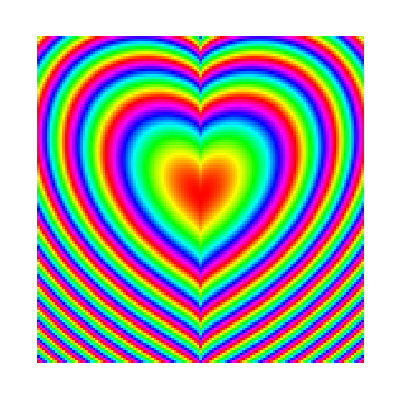

```mathematica
ArrayPlot[arr,ColorFunction->Function[z,Hue[10z+0.001]]]
```

Look up how to use ColorData functions as a ColorFunction

```mathematica
ColorData["Rainbow"]
```

How to generate nested figures like the following? (See hint below the image.)

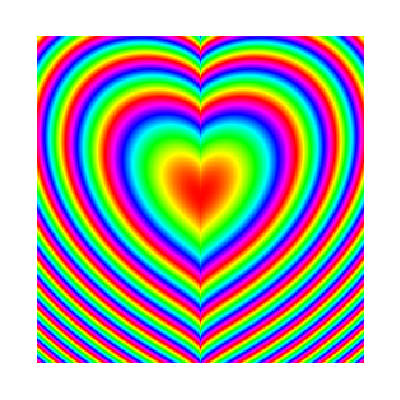

Play with the following table. What are different ways to get many colors in the list? What makes the colors periodically cycle?

```mathematica
Table[Hue[z+0.001],{z,0,2,0.1}]
```

REFLECT: Explain mathematically why we get what we see.

##### Linear recurrences

a[n+1] = a[n] + a[n-1]

```mathematica
data=NestList[
{#[[1]]+#[[2]],#[[1]]}&,
{1.,0.},(* initial values *)
100];
```

```mathematica
First/@data//
Take[#,10]&//
ListPlot
```

Differences and ratios of successive numbers are elementary ways to analyze a sequence. Sometimes patterns emerge, which can lead to conjectures and proofs.

```mathematica
First/@data//
Take[#,10]&//
Differences//
ListPlot
```

```mathematica
somedata=Take[First/@data,10];
{somedata,
somedata//Differences
}//
ListPlot
```

```mathematica
First/@data//Ratios//ListLinePlot
```

```mathematica
ratio=First/@data//Ratios//Last
```

```mathematica
ratio0=RootApproximant[ratio]
```

```mathematica
(First/@data-ratio0^(Range[1-Length@data,0])data[[-1,1]])/(First/@data)//Abs//ListLogPlot
```

a[n+1] = 2 a[n] + a[n-1]

```mathematica
data=NestList[
{2#[[1]]+#[[2]],#[[1]]}&,
{1.,0.},
100];
```

```mathematica
First/@data//Ratios//ListLinePlot
```

```mathematica
ratio=First/@data//Ratios//Last
```

2.41421

```mathematica
ratio0=RootApproximant[ratio]
```

```mathematica
(First/@data-ratio0^(Range[1-Length@data,0])data[[-1,1]])/(First/@data)//
Abs//
ListLogPlot
```

##### Nonlinear recurrences

This is based on the logistic map in the form f(x)=r x (1-x), where r is a parameter to be varied (see exercise 27.4 in which r=4). We will explore the sequence of values generated by repeatedly applying f to its output:
	x_0,f(x_0),f(f(x_0)),f(f(f(x_0))),... ; x_(n+1)=f(x_n).

Note: r must be in the range 0<=r<=4. Why?

{0.5,0.625,0.585938,0.606537,0.596625,0.601659,0.599164,0.600416,0.599791,0.600104,0.599948,0.600026,0.599987,0.600007,0.599997,0.600002,0.599999,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6}

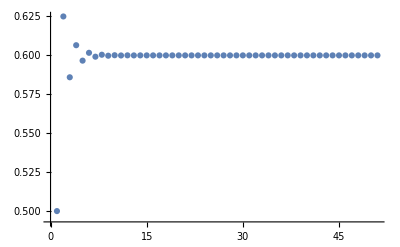

```mathematica
data=NestList[
2.5 #(1-#)&,(* This is the logistic map: What is r here? *)
0.5, (* start value *)
50]; (* number of iterations *)
data//ListPlot[#,PlotRange->All]&
```

{0.1,0.18,0.2952,0.416114,0.485926,0.499604,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

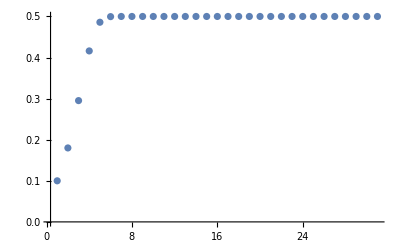

```mathematica
data=NestList[
2. #(1-#)&, (* What is r now? *)
0.1,30];
data
data//ListPlot[#,PlotRange->All]&
```

```mathematica
data=FixedPointList[2. #(1-#)&,0.7,100];
data//ListPlot[#,PlotRange->All]&
```

“Bifurcation”

```mathematica
data=Join@@Table[Thread[{r,Drop[NestList[r #(1-#)&,RandomReal[],200],100]}],{r,1,4,1/2^7}];
data//ListPlot
```

```mathematica
Manipulate[
NestList[r #(1-#)&,0.7111,200]//
ListPlot[#,PlotRange->{0,1}]&,
{r,1,4} (* 3.84 *)
]
```

##### Fold

```mathematica
Fold[
#+
If[EvenQ[#2],
4/(2#2+1),
-4/(2#2+1)
]&,
4,(* compare decimal-point *)
Range[10] 
]
```

```mathematica
FoldList[Plus,0,Range[10]]
```

#### Mini project

Use the the (scaled) sine map f(x)=r sin(x) in place of the logistic map r #(1-#)&, where r again is a parameter, to analyze the nonlinear recurrence
	x_(n+1)=r sin(x_n).

The logistic map takes a number x_n in the interval [0,1] and returns a number x_(n+1)=r x_n(1-x_n) in the interval [0,1] provided r is in the range 0<=r<=4. If we set the domain for the sine map f(x)=r sin(x) to be the interval [0,π], what range must r be in for
	x_(n+1)=r sin(x_n)
to also be in the interval [0,π]?

Explore the behavior of the sequences for the sine map produced for different values of r by carrying out the analysis as we did for the logistic map in the nonlinear recurrences section. Are there differences in behavior of the sine sequences for different values of r, as we saw for r>1 and r>3 in the logistic map. Approximately where do those transitions occur for the sine map? Describe what differences you see at those transitions.

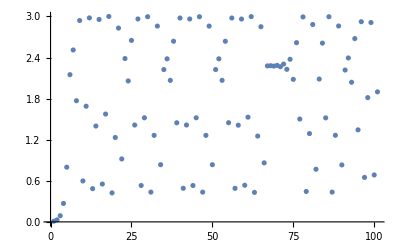

```mathematica
data=NestList[
3*Sin[#]&,(* This is the logistic map: What is r here? *)
0.01, (* start value *)
100]; (* number of iterations *)
data//ListPlot[#,PlotRange->All]&
```

```mathematica
Manipulate[
NestList[r *Sin[#]&,0.01,100]//
ListPlot[#,PlotRange->All]&,
{r,1,4} (* 3.84 *)
]
```

The function converges to 2 if r is < 2.2. The number it converges to varies but gets larger as r increases up to 2.2. However, it splits off into more and more branches as r increases past 2.2. The one original branch splits into two branches between 2.2 and 2.3 and these two branches split into four branches between 2.6 and 2.7. After that the graph becomes chaotic and unpredictable.